```mathematica
SetDirectory[NotebookDirectory[]];
<<"CppClassLayoutParser.wl";

{{Print[FileExistsQ["previos_exam_examples/Q2_W23-24_A.hpp"]]}, {□}}
```

True

{{Null},{□}}

Class “X” location: <|offset→52,line→4,col→8,tokLen→1|>

Class “Y1” location: <|offset→381,line→28,col→8,tokLen→2|>

Class “Y2” location: <|offset→609,line→43,col→8,tokLen→2|>

Class “Z” location: <|offset→839,line→57,col→8,tokLen→1|>

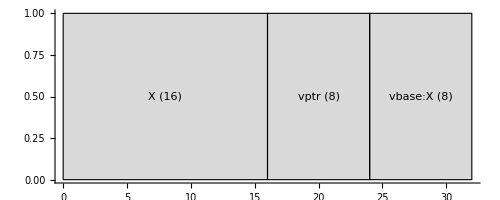

```mathematica
ParseAndDrawLayout[]
```

```mathematica
example =ComputeLayoutExample["previos_exam_examples/Q2_W23-24_A.hpp"]
```

ComputeLayoutExample[previos_exam_examples/Q2_W23-24_A.hpp]

```mathematica
classes = ParseCppToClasses["previos_exam_examples/Q2_W23-24_A.hpp"]
```

Class “X” location: <|offset→52,line→4,col→8,tokLen→1|>

Class “Y1” location: <|offset→381,line→28,col→8,tokLen→2|>

Class “Y2” location: <|offset→609,line→43,col→8,tokLen→2|>

Class “Z” location: <|offset→839,line→57,col→8,tokLen→1|>

<|X→<|AST→<|id→0x22b2376da20,kind→CXXRecordDecl,loc→<|offset→52,line→4,col→8,tokLen→1|>,range→<|begin→<|offset→45,col→1,tokLen→6|>,end→<|offset→364,line→24,col→1,tokLen→1|>|>,isReferenced→True,name→X,tagUsed→struct,completeDefinition→True,definitionData→<|canConstDefaultInit→True,copyAssign→<|hasConstParam→True,implicitHasConstParam→True,nonTrivial→True,simple→True|>,copyCtor→<|hasConstParam→True,implicitHasConstParam→True,nonTrivial→True,simple→True|>,defaultCtor→<|exists→True,nonTrivial→True,userProvided→True|>,dtor→<|irrelevant→True,simple→True,trivial→True|>,hasUserDeclaredConstructor→True,isPolymorphic→True,moveAssign→<|exists→True,nonTrivial→True,simple→True|>,moveCtor→<|exists→True,nonTrivial→True,simple→True|>|>,inner→{<|id→0x22b2376db38,kind→CXXRecordDecl,loc→<|offset→52,line→4,col→8,tokLen→1|>,range→<|begin→<|offset→45,col→1,tokLen→6|>,end→<|offset→52,col→8,tokLen→1|>|>,isImplicit→True,isReferenced→True,name→X,tagUsed→struct|>,<|id→0x22b2376dbe0,kind→FieldDecl,loc→<|offset→65,line→5,col→9,tokLen→1|>,range→<|begin→<|offset→61,col→5,tokLen→3|>,end→<|offset→65,col→9,tokLen→1|>|>,isReferenced→True,name→x,type→<|qualType→int|>|>,<|id→0x22b2376dce0,kind→CXXConstructorDecl,loc→<|offset→75,line→7,col→5,tokLen→1|>,range→<|begin→<|offset→75,col→5,tokLen→1|>,end→<|offset→140,line→11,col→5,tokLen→1|>|>,isUsed→True,name→X,mangledName→??0X@@QEAA@XZ,type→<|qualType→void ()|>,inner→{<|id→0x22b237a5ba0,kind→CompoundStmt,range→<|begin→<|offset→79,line→7,col→9,tokLen→1|>,end→<|offset→140,line→11,col→5,tokLen→1|>|>,inner→{<|id→0x22b2376e810,kind→BinaryOperator,range→<|begin→<|offset→114,line→9,col→9,tokLen→1|>,end→<|offset→118,col→13,tokLen→1|>|>,type→<|qualType→int|>,valueCategory→lvalue,opcode→=,inner→{<|id→0x22b2376e7b8,kind→MemberExpr,range→<|begin→<|offset→114,col→9,tokLen→1|>,end→<|offset→114,col→9,tokLen→1|>|>,type→<|qualType→int|>,valueCategory→lvalue,name→x,isArrow→True,referencedMemberDecl→0x22b2376dbe0,inner→{<|id→0x22b2376e7a8,kind→CXXThisExpr,range→<|begin→<|offset→114,col→9,tokLen→1|>,end→<|offset→114,col→9,tokLen→1|>|>,type→<|qualType→X *|>,valueCategory→prvalue,implicit→True|>}|>,<|id→0x22b2376e7e8,kind→IntegerLiteral,range→<|begin→<|offset→118,col→13,tokLen→1|>,end→<|offset→118,col→13,tokLen→1|>|>,type→<|qualType→int|>,valueCategory→prvalue,value→7|>}|>,<|id→0x22b237a5ab8,kind→CXXMemberCallExpr,range→<|begin→<|offset→130,line→10,col→9,tokLen→1|>,end→<|offset→132,col→11,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x22b237a5a88,kind→MemberExpr,range→<|begin→<|offset→130,col→9,tokLen→1|>,end→<|offset→130,col→9,tokLen→1|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→f,isArrow→True,referencedMemberDecl→0x22b2376df68,inner→{<|id→0x22b2376e878,kind→CXXThisExpr,range→<|begin→<|offset→130,col→9,tokLen→1|>,end→<|offset→130,col→9,tokLen→1|>|>,type→<|qualType→X *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x22b2376de80,kind→CXXConstructorDecl,loc→<|offset→147,line→12,col→5,tokLen→1|>,range→<|begin→<|offset→147,col→5,tokLen→1|>,end→<|offset→224,line→16,col→5,tokLen→1|>|>,isUsed→True,name→X,mangledName→??0X@@QEAA@H@Z,type→<|qualType→void (int)|>,inner→{<|id→0x22b2376dda8,kind→ParmVarDecl,loc→<|offset→153,line→12,col→11,tokLen→3|>,range→<|begin→<|offset→149,col→7,tokLen→3|>,end→<|offset→153,col→11,tokLen→3|>|>,isUsed→True,name→val,type→<|qualType→int|>|>,<|id→0x22b237a5de8,kind→CompoundStmt,range→<|begin→<|offset→158,col→16,tokLen→1|>,end→<|offset→224,line→16,col→5,tokLen→1|>|>,inner→{<|id→0x22b237a5d20,kind→BinaryOperator,range→<|begin→<|offset→196,line→14,col→9,tokLen→1|>,end→<|offset→200,col→13,tokLen→3|>|>,type→<|qualType→int|>,valueCategory→lvalue,opcode→=,inner→{<|id→0x22b237a5cb8,kind→MemberExpr,range→<|begin→<|offset→196,col→9,tokLen→1|>,end→<|offset→196,col→9,tokLen→1|>|>,type→<|qualType→int|>,valueCategory→lvalue,name→x,isArrow→True,referencedMemberDecl→0x22b2376dbe0,inner→{<|id→0x22b237a5ca8,kind→CXXThisExpr,range→<|begin→<|offset→196,col→9,tokLen→1|>,end→<|offset→196,col→9,tokLen→1|>|>,type→<|qualType→X *|>,valueCategory→prvalue,implicit→True|>}|>,<|id→0x22b237a5d08,kind→ImplicitCastExpr,range→<|begin→<|offset→200,col→13,tokLen→3|>,end→<|offset→200,col→13,tokLen→3|>|>,type→<|qualType→int|>,valueCategory→prvalue,castKind→LValueToRValue,inner→{<|id→0x22b237a5ce8,kind→DeclRefExpr,range→<|begin→<|offset→200,col→13,tokLen→3|>,end→<|offset→200,col→13,tokLen→3|>|>,type→<|qualType→int|>,valueCategory→lvalue,referencedDecl→<|id→0x22b2376dda8,kind→ParmVarDecl,name→val,type→<|qualType→int|>|>|>}|>}|>,<|id→0x22b237a5dc8,kind→CXXMemberCallExpr,range→<|begin→<|offset→214,line→15,col→9,tokLen→1|>,end→<|offset→216,col→11,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x22b237a5d98,kind→MemberExpr,range→<|begin→<|offset→214,col→9,tokLen→1|>,end→<|offset→214,col→9,tokLen→1|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→f,isArrow→True,referencedMemberDecl→0x22b2376df68,inner→{<|id→0x22b237a5d88,kind→CXXThisExpr,range→<|begin→<|offset→214,col→9,tokLen→1|>,end→<|offset→214,col→9,tokLen→1|>|>,type→<|qualType→X *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x22b2376df68,kind→CXXMethodDecl,loc→<|offset→244,line→17,col→18,tokLen→1|>,range→<|begin→<|offset→231,col→5,tokLen→7|>,end→<|offset→297,line→20,col→5,tokLen→1|>|>,isUsed→True,name→f,mangledName→?f@X@@UEAAXXZ,type→<|qualType→void ()|>,virtual→True,inner→{<|id→0x22b237a5ed0,kind→CompoundStmt,range→<|begin→<|offset→248,line→17,col→22,tokLen→1|>,end→<|offset→297,line→20,col→5,tokLen→1|>|>,inner→{<|id→0x22b237a5eb0,kind→CXXMemberCallExpr,range→<|begin→<|offset→286,line→19,col→9,tokLen→2|>,end→<|offset→289,col→12,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x22b237a5e80,kind→MemberExpr,range→<|begin→<|offset→286,col→9,tokLen→2|>,end→<|offset→286,col→9,tokLen→2|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→g2,isArrow→True,referencedMemberDecl→0x22b2376e030,inner→{<|id→0x22b237a5e70,kind→CXXThisExpr,range→<|begin→<|offset→286,col→9,tokLen→2|>,end→<|offset→286,col→9,tokLen→2|>|>,type→<|qualType→X *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x22b2376e030,kind→CXXMethodDecl,loc→<|offset→317,line→21,col→18,tokLen→2|>,range→<|begin→<|offset→304,col→5,tokLen→7|>,end→<|offset→361,line→23,col→9,tokLen→1|>|>,isUsed→True,name→g2,mangledName→?g2@X@@UEAAXXZ,type→<|qualType→void ()|>,virtual→True,inner→{<|id→0x22b237a5f90,kind→CompoundStmt,range→<|begin→<|offset→322,line→21,col→23,tokLen→1|>,end→<|offset→361,line→23,col→9,tokLen→1|>|>|>}|>,<|id→0x22b2376e1e0,kind→CXXMethodDecl,loc→<|offset→52,line→4,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,isImplicit→True,name→operator=,mangledName→??4X@@QEAAAEAU0@AEBU0@@Z,type→<|qualType→X &(const X &)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x22b2376e310,kind→ParmVarDecl,loc→<|offset→52,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,type→<|qualType→const X &|>|>}|>,<|id→0x22b2376e3f0,kind→CXXMethodDecl,loc→<|offset→52,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,isImplicit→True,name→operator=,mangledName→??4X@@QEAAAEAU0@$$QEAU0@@Z,type→<|qualType→X &(X &&)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x22b2376e520,kind→ParmVarDecl,loc→<|offset→52,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,type→<|qualType→X &&|>|>}|>,<|id→0x22b2376e5c0,kind→CXXDestructorDecl,loc→<|offset→52,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,isImplicit→True,name→~X,mangledName→??_DX@@QEAAXXZ,type→<|qualType→void ()|>,inline→True,explicitlyDefaulted→default|>,<|id→0x22b237a7e88,kind→CXXConstructorDecl,loc→<|offset→52,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,isImplicit→True,name→X,mangledName→??0X@@QEAA@AEBU0@@Z,type→<|qualType→void (const X &)|>,inline→True,constexpr→True,explicitlyDefaulted→default,inner→{<|id→0x22b237a7fc0,kind→ParmVarDecl,loc→<|offset→52,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,type→<|qualType→const X &|>|>}|>,<|id→0x22b237a8048,kind→CXXConstructorDecl,loc→<|offset→52,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,isImplicit→True,name→X,mangledName→??0X@@QEAA@$$QEAU0@@Z,type→<|qualType→void (X &&)|>,inline→True,constexpr→True,explicitlyDefaulted→default,inner→{<|id→0x22b237a8180,kind→ParmVarDecl,loc→<|offset→52,col→8,tokLen→1|>,range→<|begin→<|offset→52,col→8,tokLen→1|>,end→<|offset→52,col→8,tokLen→1|>|>,type→<|qualType→X &&|>|>}|>}|>,Bases→{},Fields→{{x,int}}|>,Y1→<|AST→<|id→0x22b237a5fa0,kind→CXXRecordDecl,loc→<|offset→381,line→28,col→8,tokLen→2|>,range→<|begin→<|offset→374,col→1,tokLen→6|>,end→<|offset→594,line→40,col→1,tokLen→1|>|>,isReferenced→True,name→Y1,tagUsed→struct,completeDefinition→True,definitionData→<|canConstDefaultInit→True,copyAssign→<|hasConstParam→True,implicitHasConstParam→True,nonTrivial→True,simple→True|>,copyCtor→<|hasConstParam→True,implicitHasConstParam→True,nonTrivial→True,simple→True|>,defaultCtor→<|exists→True,nonTrivial→True,userProvided→True|>,dtor→<|irrelevant→True,simple→True,trivial→True|>,hasUserDeclaredConstructor→True,isPolymorphic→True,moveAssign→<|exists→True,nonTrivial→True,simple→True|>,moveCtor→<|exists→True,nonTrivial→True,simple→True|>|>,bases→{<|access→public,isVirtual→True,type→<|qualType→X|>,writtenAccess→none|>},inner→{<|id→0x22b237a6110,kind→CXXRecordDecl,loc→<|offset→381,line→28,col→8,tokLen→2|>,range→<|begin→<|offset→374,col→1,tokLen→6|>,end→<|offset→381,col→8,tokLen→2|>|>,isImplicit→True,isReferenced→True,name→Y1,tagUsed→struct|>,<|id→0x22b237a6208,kind→CXXConstructorDecl,loc→<|offset→403,line→29,col→5,tokLen→2|>,range→<|begin→<|offset→403,col→5,tokLen→2|>,end→<|offset→460,line→32,col→5,tokLen→1|>|>,isUsed→True,name→Y1,mangledName→??0Y1@@QEAA@XZ,type→<|qualType→void ()|>,inner→{<|kind→CXXCtorInitializer,baseInit→<|qualType→X|>,inner→{<|id→0x22b237a8240,kind→CXXConstructExpr,range→<|begin→<|offset→409,line→29,col→11,tokLen→1|>,end→<|offset→412,col→14,tokLen→1|>|>,type→<|qualType→X|>,valueCategory→prvalue,ctorType→<|qualType→void (int)|>,hadMultipleCandidates→True,constructionKind→virtual base,inner→{<|id→0x22b237a6a28,kind→IntegerLiteral,range→<|begin→<|offset→411,col→13,tokLen→1|>,end→<|offset→411,col→13,tokLen→1|>|>,type→<|qualType→int|>,valueCategory→prvalue,value→2|>}|>}|>,<|id→0x22b237a84a8,kind→CompoundStmt,range→<|begin→<|offset→414,col→16,tokLen→1|>,end→<|offset→460,line→32,col→5,tokLen→1|>|>,inner→{<|id→0x22b237a83c8,kind→CXXMemberCallExpr,range→<|begin→<|offset→450,line→31,col→9,tokLen→1|>,end→<|offset→452,col→11,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x22b237a8398,kind→MemberExpr,range→<|begin→<|offset→450,col→9,tokLen→1|>,end→<|offset→450,col→9,tokLen→1|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→f,isArrow→True,referencedMemberDecl→0x22b237a62d8,inner→{<|id→0x22b237a8388,kind→CXXThisExpr,range→<|begin→<|offset→450,col→9,tokLen→1|>,end→<|offset→450,col→9,tokLen→1|>|>,type→<|qualType→Y1 *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x22b237a62d8,kind→CXXMethodDecl,loc→<|offset→480,line→33,col→18,tokLen→1|>,range→<|begin→<|offset→467,col→5,tokLen→7|>,end→<|offset→534,line→36,col→5,tokLen→1|>|>,isUsed→True,name→f,mangledName→?f@Y1@@UEAAXXZ,type→<|qualType→void ()|>,virtual→True,inner→{<|id→0x22b237a8588,kind→CompoundStmt,range→<|begin→<|offset→484,line→33,col→22,tokLen→1|>,end→<|offset→534,line→36,col→5,tokLen→1|>|>,inner→{<|id→0x22b237a8568,kind→CXXMemberCallExpr,range→<|begin→<|offset→523,line→35,col→9,tokLen→2|>,end→<|offset→526,col→12,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x22b237a8538,kind→MemberExpr,range→<|begin→<|offset→523,col→9,tokLen→2|>,end→<|offset→523,col→9,tokLen→2|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→g1,isArrow→True,referencedMemberDecl→0x22b237a63d0,inner→{<|id→0x22b237a8528,kind→CXXThisExpr,range→<|begin→<|offset→523,col→9,tokLen→2|>,end→<|offset→523,col→9,tokLen→2|>|>,type→<|qualType→Y1 *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x22b237a63d0,kind→CXXMethodDecl,loc→<|offset→554,line→37,col→18,tokLen→2|>,range→<|begin→<|offset→541,col→5,tokLen→7|>,end→<|offset→591,line→39,col→5,tokLen→1|>|>,isUsed→True,name→g1,mangledName→?g1@Y1@@UEAAXXZ,type→<|qualType→void ()|>,virtual→True,inner→{<|id→0x22b237a8640,kind→CompoundStmt,range→<|begin→<|offset→559,line→37,col→23,tokLen→1|>,end→<|offset→591,line→39,col→5,tokLen→1|>|>|>}|>,<|id→0x22b237a6550,kind→CXXMethodDecl,loc→<|offset→381,line→28,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,isImplicit→True,name→operator=,mangledName→??4Y1@@QEAAAEAU0@AEBU0@@Z,type→<|qualType→Y1 &(const Y1 &)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x22b237a6680,kind→ParmVarDecl,loc→<|offset→381,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,type→<|qualType→const Y1 &|>|>}|>,<|id→0x22b237a6760,kind→CXXMethodDecl,loc→<|offset→381,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,isImplicit→True,name→operator=,mangledName→??4Y1@@QEAAAEAU0@$$QEAU0@@Z,type→<|qualType→Y1 &(Y1 &&)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x22b237a6890,kind→ParmVarDecl,loc→<|offset→381,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,type→<|qualType→Y1 &&|>|>}|>,<|id→0x22b237a6930,kind→CXXDestructorDecl,loc→<|offset→381,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,isImplicit→True,name→~Y1,mangledName→??_DY1@@QEAAXXZ,type→<|qualType→void ()|>,inline→True,explicitlyDefaulted→default|>,<|id→0x22b237aa3d0,kind→CXXConstructorDecl,loc→<|offset→381,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,isImplicit→True,name→Y1,mangledName→??0Y1@@QEAA@AEBU0@@Z,type→<|qualType→void (const Y1 &)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x22b237aa500,kind→ParmVarDecl,loc→<|offset→381,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,type→<|qualType→const Y1 &|>|>}|>,<|id→0x22b237aa588,kind→CXXConstructorDecl,loc→<|offset→381,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,isImplicit→True,name→Y1,mangledName→??0Y1@@QEAA@$$QEAU0@@Z,type→<|qualType→void (Y1 &&)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x22b237aa6c0,kind→ParmVarDecl,loc→<|offset→381,col→8,tokLen→2|>,range→<|begin→<|offset→381,col→8,tokLen→2|>,end→<|offset→381,col→8,tokLen→2|>|>,type→<|qualType→Y1 &&|>|>}|>}|>,Bases→{{X,True}},Fields→{}|>,Y2→<|AST→<|id→0x22b237a8650,kind→CXXRecordDecl,loc→<|offset→609,line→43,col→8,tokLen→2|>,range→<|begin→<|offset→602,col→1,tokLen→6|>,end→<|offset→826,line→55,col→1,tokLen→1|>|>,isReferenced→True,name→Y2,tagUsed→struct,completeDefinition→True,definitionData→<|canConstDefaultInit→True,copyAssign→<|hasConstParam→True,implicitHasConstParam→True,nonTrivial→True,simple→True|>,copyCtor→<|hasConstParam→True,implicitHasConstParam→True,nonTrivial→True,simple→True|>,defaultCtor→<|exists→True,nonTrivial→True,userProvided→True|>,dtor→<|irrelevant→True,simple→True,trivial→True|>,hasUserDeclaredConstructor→True,isPolymorphic→True,moveAssign→<|exists→True,nonTrivial→True,simple→True|>,moveCtor→<|exists→True,nonTrivial→True,simple→True|>|>,bases→{<|access→public,isVirtual→True,type→<|qualType→X|>,writtenAccess→none|>},inner→{<|id→0x22b237a87c0,kind→CXXRecordDecl,loc→<|offset→609,line→43,col→8,tokLen→2|>,range→<|begin→<|offset→602,col→1,tokLen→6|>,end→<|offset→609,col→8,tokLen→2|>|>,isImplicit→True,isReferenced→True,name→Y2,tagUsed→struct|>,<|id→0x22b237a88b8,kind→CXXConstructorDecl,loc→<|offset→631,line→44,col→5,tokLen→2|>,range→<|begin→<|offset→631,col→5,tokLen→2|>,end→<|offset→688,line→47,col→5,tokLen→1|>|>,isUsed→True,name→Y2,mangledName→??0Y2@@QEAA@XZ,type→<|qualType→void ()|>,inner→{<|kind→CXXCtorInitializer,baseInit→<|qualType→X|>,inner→{<|id→0x22b237a93a0,kind→CXXConstructExpr,range→<|begin→<|offset→637,line→44,col→11,tokLen→1|>,end→<|offset→640,col→14,tokLen→1|>|>,type→<|qualType→X|>,valueCategory→prvalue,ctorType→<|qualType→void (int)|>,hadMultipleCandidates→True,constructionKind→virtual base,inner→{<|id→0x22b237a9348,kind→IntegerLiteral,range→<|begin→<|offset→639,col→13,tokLen→1|>,end→<|offset→639,col→13,tokLen→1|>|>,type→<|qualType→int|>,valueCategory→prvalue,value→2|>}|>}|>,<|id→0x22b237a9580,kind→CompoundStmt,range→<|begin→<|offset→642,col→16,tokLen→1|>,end→<|offset→688,line→47,col→5,tokLen→1|>|>,inner→{<|id→0x22b237a94a0,kind→CXXMemberCallExpr,range→<|begin→<|offset→678,line→46,col→9,tokLen→1|>,end→<|offset→680,col→11,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x22b237a9470,kind→MemberExpr,range→<|begin→<|offset→678,col→9,tokLen→1|>,end→<|offset→678,col→9,tokLen→1|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→f,isArrow→True,referencedMemberDecl→0x22b237a8988,inner→{<|id→0x22b237a9460,kind→CXXThisExpr,range→<|begin→<|offset→678,col→9,tokLen→1|>,end→<|offset→678,col→9,tokLen→1|>|>,type→<|qualType→Y2 *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x22b237a8988,kind→CXXMethodDecl,loc→<|offset→708,line→48,col→18,tokLen→1|>,range→<|begin→<|offset→695,col→5,tokLen→7|>,end→<|offset→762,line→51,col→5,tokLen→1|>|>,isUsed→True,name→f,mangledName→?f@Y2@@UEAAXXZ,type→<|qualType→void ()|>,virtual→True,inner→{<|id→0x22b237a9660,kind→CompoundStmt,range→<|begin→<|offset→712,line→48,col→22,tokLen→1|>,end→<|offset→762,line→51,col→5,tokLen→1|>|>,inner→{<|id→0x22b237a9640,kind→CXXMemberCallExpr,range→<|begin→<|offset→751,line→50,col→9,tokLen→2|>,end→<|offset→754,col→12,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x22b237a9610,kind→MemberExpr,range→<|begin→<|offset→751,col→9,tokLen→2|>,end→<|offset→751,col→9,tokLen→2|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→g2,isArrow→True,referencedMemberDecl→0x22b237a8a80,inner→{<|id→0x22b237a9600,kind→CXXThisExpr,range→<|begin→<|offset→751,col→9,tokLen→2|>,end→<|offset→751,col→9,tokLen→2|>|>,type→<|qualType→Y2 *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x22b237a8a80,kind→CXXMethodDecl,loc→<|offset→782,line→52,col→18,tokLen→2|>,range→<|begin→<|offset→769,col→5,tokLen→7|>,end→<|offset→823,line→54,col→5,tokLen→1|>|>,isUsed→True,name→g2,mangledName→?g2@Y2@@UEAAXXZ,type→<|qualType→void ()|>,virtual→True,inner→{<|id→0x22b237a9698,kind→CompoundStmt,range→<|begin→<|offset→787,line→52,col→23,tokLen→1|>,end→<|offset→823,line→54,col→5,tokLen→1|>|>|>}|>,<|id→0x22b237a8c00,kind→CXXMethodDecl,loc→<|offset→609,line→43,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,isImplicit→True,name→operator=,mangledName→??4Y2@@QEAAAEAU0@AEBU0@@Z,type→<|qualType→Y2 &(const Y2 &)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x22b237a8d30,kind→ParmVarDecl,loc→<|offset→609,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,type→<|qualType→const Y2 &|>|>}|>,<|id→0x22b237a9088,kind→CXXMethodDecl,loc→<|offset→609,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,isImplicit→True,name→operator=,mangledName→??4Y2@@QEAAAEAU0@$$QEAU0@@Z,type→<|qualType→Y2 &(Y2 &&)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x22b237a91b0,kind→ParmVarDecl,loc→<|offset→609,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,type→<|qualType→Y2 &&|>|>}|>,<|id→0x22b237a9250,kind→CXXDestructorDecl,loc→<|offset→609,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,isImplicit→True,name→~Y2,mangledName→??_DY2@@QEAAXXZ,type→<|qualType→void ()|>,inline→True,explicitlyDefaulted→default|>,<|id→0x22b237aa7d8,kind→CXXConstructorDecl,loc→<|offset→609,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,isImplicit→True,name→Y2,mangledName→??0Y2@@QEAA@AEBU0@@Z,type→<|qualType→void (const Y2 &)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x22b237aa910,kind→ParmVarDecl,loc→<|offset→609,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,type→<|qualType→const Y2 &|>|>}|>,<|id→0x22b237aa998,kind→CXXConstructorDecl,loc→<|offset→609,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,isImplicit→True,name→Y2,mangledName→??0Y2@@QEAA@$$QEAU0@@Z,type→<|qualType→void (Y2 &&)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x22b237aaad0,kind→ParmVarDecl,loc→<|offset→609,col→8,tokLen→2|>,range→<|begin→<|offset→609,col→8,tokLen→2|>,end→<|offset→609,col→8,tokLen→2|>|>,type→<|qualType→Y2 &&|>|>}|>}|>,Bases→{{X,True}},Fields→{}|>,Z→<|AST→<|id→0x22b237a96a8,kind→CXXRecordDecl,loc→<|offset→839,line→57,col→8,tokLen→1|>,range→<|begin→<|offset→832,col→1,tokLen→6|>,end→<|offset→1046,line→69,col→1,tokLen→1|>|>,name→Z,tagUsed→struct,completeDefinition→True,definitionData→<|canConstDefaultInit→True,copyAssign→<|hasConstParam→True,implicitHasConstParam→True,nonTrivial→True,simple→True|>,copyCtor→<|hasConstParam→True,implicitHasConstParam→True,needsImplicit→True,nonTrivial→True,simple→True|>,defaultCtor→<|exists→True,nonTrivial→True,userProvided→True|>,dtor→<|irrelevant→True,simple→True,trivial→True|>,hasUserDeclaredConstructor→True,isPolymorphic→True,moveAssign→<|exists→True,nonTrivial→True,simple→True|>,moveCtor→<|exists→True,needsImplicit→True,nonTrivial→True,simple→True|>|>,bases→{<|access→public,type→<|qualType→Y1|>,writtenAccess→none|>,<|access→public,type→<|qualType→Y2|>,writtenAccess→none|>},inner→{<|id→0x22b237a9860,kind→CXXRecordDecl,loc→<|offset→839,line→57,col→8,tokLen→1|>,range→<|begin→<|offset→832,col→1,tokLen→6|>,end→<|offset→839,col→8,tokLen→1|>|>,isImplicit→True,isReferenced→True,name→Z,tagUsed→struct|>,<|id→0x22b237a9958,kind→CXXConstructorDecl,loc→<|offset→857,line→58,col→5,tokLen→1|>,range→<|begin→<|offset→857,col→5,tokLen→1|>,end→<|offset→910,line→61,col→5,tokLen→1|>|>,name→Z,mangledName→??0Z@@QEAA@XZ,type→<|qualType→void ()|>,inner→{<|kind→CXXCtorInitializer,baseInit→<|qualType→X|>,inner→{<|id→0x22b237aa378,kind→CXXConstructExpr,range→<|begin→<|offset→857,line→58,col→5,tokLen→1|>,end→<|offset→857,col→5,tokLen→1|>|>,type→<|qualType→X|>,valueCategory→prvalue,ctorType→<|qualType→void ()|>,hadMultipleCandidates→True,constructionKind→virtual base|>}|>,<|kind→CXXCtorInitializer,baseInit→<|qualType→Y1|>,inner→{<|id→0x22b237aa780,kind→CXXConstructExpr,range→<|begin→<|offset→857,col→5,tokLen→1|>,end→<|offset→857,col→5,tokLen→1|>|>,type→<|qualType→Y1|>,valueCategory→prvalue,ctorType→<|qualType→void ()|>,hadMultipleCandidates→True,constructionKind→non-virtual base|>}|>,<|kind→CXXCtorInitializer,baseInit→<|qualType→Y2|>,inner→{<|id→0x22b237aab90,kind→CXXConstructExpr,range→<|begin→<|offset→857,col→5,tokLen→1|>,end→<|offset→857,col→5,tokLen→1|>|>,type→<|qualType→Y2|>,valueCategory→prvalue,ctorType→<|qualType→void ()|>,hadMultipleCandidates→True,constructionKind→non-virtual base|>}|>,<|id→0x22b237aad88,kind→CompoundStmt,range→<|begin→<|offset→861,col→9,tokLen→1|>,end→<|offset→910,line→61,col→5,tokLen→1|>|>,inner→{<|id→0x22b237aaca8,kind→CXXMemberCallExpr,range→<|begin→<|offset→896,line→60,col→9,tokLen→1|>,end→<|offset→898,col→11,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x22b237aac78,kind→MemberExpr,range→<|begin→<|offset→896,col→9,tokLen→1|>,end→<|offset→896,col→9,tokLen→1|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→f,isArrow→True,referencedMemberDecl→0x22b237a9a28,inner→{<|id→0x22b237aac68,kind→CXXThisExpr,range→<|begin→<|offset→896,col→9,tokLen→1|>,end→<|offset→896,col→9,tokLen→1|>|>,type→<|qualType→Z *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x22b237a9a28,kind→CXXMethodDecl,loc→<|offset→930,line→62,col→18,tokLen→1|>,range→<|begin→<|offset→917,col→5,tokLen→7|>,end→<|offset→983,line→65,col→5,tokLen→1|>|>,isUsed→True,name→f,mangledName→?f@Z@@UEAAXXZ,type→<|qualType→void ()|>,virtual→True,inner→{<|id→0x22b237aae68,kind→CompoundStmt,range→<|begin→<|offset→934,line→62,col→22,tokLen→1|>,end→<|offset→983,line→65,col→5,tokLen→1|>|>,inner→{<|id→0x22b237aae48,kind→CXXMemberCallExpr,range→<|begin→<|offset→972,line→64,col→9,tokLen→2|>,end→<|offset→975,col→12,tokLen→1|>|>,type→<|qualType→void|>,valueCategory→prvalue,inner→{<|id→0x22b237aae18,kind→MemberExpr,range→<|begin→<|offset→972,col→9,tokLen→2|>,end→<|offset→972,col→9,tokLen→2|>|>,type→<|qualType→<bound member function type>|>,valueCategory→prvalue,name→g1,isArrow→True,referencedMemberDecl→0x22b237a9b20,inner→{<|id→0x22b237aae08,kind→CXXThisExpr,range→<|begin→<|offset→972,col→9,tokLen→2|>,end→<|offset→972,col→9,tokLen→2|>|>,type→<|qualType→Z *|>,valueCategory→prvalue,implicit→True|>}|>}|>}|>}|>,<|id→0x22b237a9b20,kind→CXXMethodDecl,loc→<|offset→1003,line→66,col→18,tokLen→2|>,range→<|begin→<|offset→990,col→5,tokLen→7|>,end→<|offset→1043,line→68,col→5,tokLen→1|>|>,isUsed→True,name→g1,mangledName→?g1@Z@@UEAAXXZ,type→<|qualType→void ()|>,virtual→True,inner→{<|id→0x22b237aaea0,kind→CompoundStmt,range→<|begin→<|offset→1008,line→66,col→23,tokLen→1|>,end→<|offset→1043,line→68,col→5,tokLen→1|>|>|>}|>,<|id→0x22b237a9ca0,kind→CXXMethodDecl,loc→<|offset→839,line→57,col→8,tokLen→1|>,range→<|begin→<|offset→839,col→8,tokLen→1|>,end→<|offset→839,col→8,tokLen→1|>|>,isImplicit→True,name→operator=,mangledName→??4Z@@QEAAAEAU0@AEBU0@@Z,type→<|qualType→Z &(const Z &)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x22b237a9dd0,kind→ParmVarDecl,loc→<|offset→839,col→8,tokLen→1|>,range→<|begin→<|offset→839,col→8,tokLen→1|>,end→<|offset→839,col→8,tokLen→1|>|>,type→<|qualType→const Z &|>|>}|>,<|id→0x22b237a9eb0,kind→CXXMethodDecl,loc→<|offset→839,col→8,tokLen→1|>,range→<|begin→<|offset→839,col→8,tokLen→1|>,end→<|offset→839,col→8,tokLen→1|>|>,isImplicit→True,name→operator=,mangledName→??4Z@@QEAAAEAU0@$$QEAU0@@Z,type→<|qualType→Z &(Z &&)|>,inline→True,explicitlyDefaulted→default,inner→{<|id→0x22b237a9fe0,kind→ParmVarDecl,loc→<|offset→839,col→8,tokLen→1|>,range→<|begin→<|offset→839,col→8,tokLen→1|>,end→<|offset→839,col→8,tokLen→1|>|>,type→<|qualType→Z &&|>|>}|>,<|id→0x22b237aa288,kind→CXXDestructorDecl,loc→<|offset→839,col→8,tokLen→1|>,range→<|begin→<|offset→839,col→8,tokLen→1|>,end→<|offset→839,col→8,tokLen→1|>|>,isImplicit→True,name→~Z,mangledName→??_DZ@@QEAAXXZ,type→<|qualType→void ()|>,inline→True,explicitlyDefaulted→default|>}|>,Bases→{{Y1,False},{Y2,False}},Fields→{}|>|>